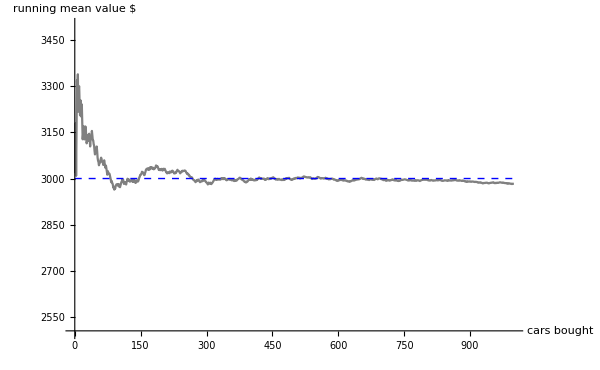

```mathematica
n = 1000;
vData=RandomVariate[UniformDistribution[{2000,4000}],{n}];
vMean=Accumulate[vData]/Table[i,{i,1,n}];
Show[ListLinePlot[vMean,PlotRange->{Automatic,{2500,3500}},PlotStyle->Gray,Epilog->{Dashed,Blue,Line[{{0,3000},{n,3000}}]},BaseStyle->{FontSize->16},AxesLabel->{"cars bought ","running mean value $ "}],ImageSize->600]
```